## Numerical Example Ambartsumyan et al. CMAME (2020) :

### Displacement :

```mathematica
u[x_,y_]:={x,y}
```

Dirichlet boundary conditions : (they are not homogeneous)

```mathematica
u[0,y]
```

{0,y}

```mathematica
u[1,y]
```

{1,y}

```mathematica
u[x,0]
```

{x,0}

```mathematica
u[x,1]
```

{x,1}

ContourPlot of the Magnitude of the displacement (Euclidean norm) :

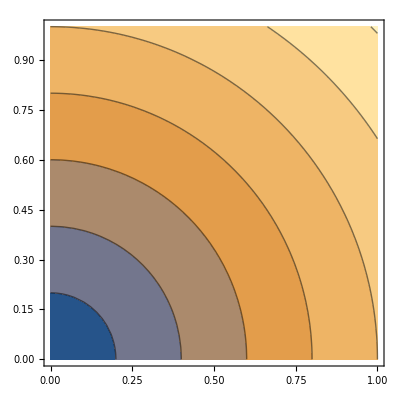

```mathematica
ContourPlot[Sqrt[(x)^2+(y)^2],{x,0,1},{y,0,1}]
```

### Pressure:

```mathematica
p[x_,t_]:=t x
```

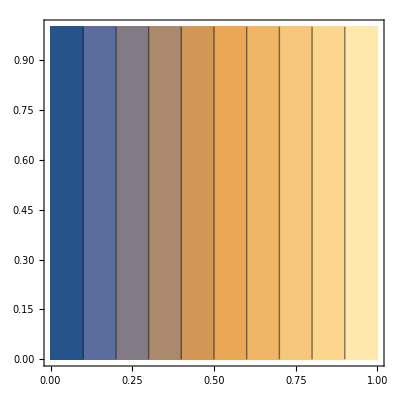

```mathematica
ContourPlot[p[x,0.001],{x,0,1},{y,0,1}]
```

### Elastic Stress:

```mathematica
{D[(x), x],D[(x), y]}//Simplify
```

{1,0}

```mathematica
{D[(y), x],D[(y), y]}//Simplify
```

{0,1}

```mathematica
Gradu:={{1,0},{0,1}}
```

Let us define ϵ (u) :

```mathematica
1/2*(Gradu+Transpose[Gradu])//Simplify
```

{{1,0},{0,1}}

```mathematica
EE:=1
nu:=0.2
mu=μ
lambda=λ
```

μ

λ

Let us compute the stress σ= A^-1 ϵ(u): (Using the expression for A^-1 given in equation (3 . 2 . 9) of Ambartsumyan PhD. Thesis)

```mathematica
2 mu {{1,0},{0,1}}+lambda {{2,0},{0,2}}//Simplify
```

{{2 (λ+μ),0},{0,2 (λ+μ)}}

Let us define the stress function as the previous expression :

```mathematica
Sigmae:={{2 (λ+μ),0},{0,2 (λ+μ)}}
```

### Stress:

```mathematica
Sigmae-alpha {{p[x,t],0},{0,p[x,t]}}//Simplify
```

{{-alpha t x+2 (λ+μ),0},{0,-alpha t x+2 (λ+μ)}}

```mathematica
Sigma[x_,t_]:={{-alpha t x+2 (λ+μ),0},{0,-alpha t x+2 (λ+μ)}}
```

ContourPlot of the Magnitude of the first row of σ :

lambda: 	E*nu/((1+nu)(1-2 nu))

```mathematica
0.2/((1.2)(1-0.4))
```

0.277778

mu:		E/(2(1+nu))

```mathematica
1/2.4
```

0.416667

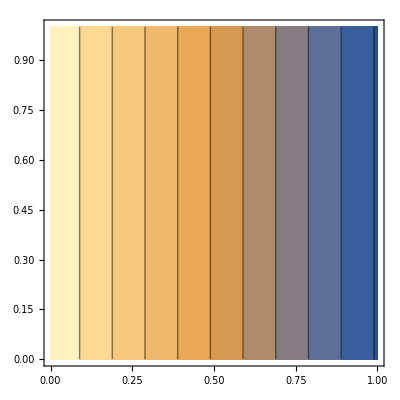

```mathematica
ContourPlot[Sqrt[(-alpha t x+2 (λ+μ))^2+(0)^2]/.{t->0.001,λ ->EE*nu/((1+nu)(1-2 nu)),μ->EE/(2(1+nu)),alpha->1},{x,0,1},{y,0,1}]
```

ContourPlot of the Magnitude of the second row of σ :

```mathematica
ContourPlot[Sqrt[(0)^2+(-alpha t x+2 (λ+μ))^2]/.{t->0.001,λ ->EE*nu/((1+nu)(1-2 nu)),μ->EE/(2(1+nu)),alpha->1},{x,0,1},{y,0,1}]
```

-Graphics-

### Rotation :

```mathematica
1/2*(Gradu-Transpose[Gradu])//Simplify
```

{{0,0},{0,0}}

ContourPlot of the element in the first row and second column of the rotation:

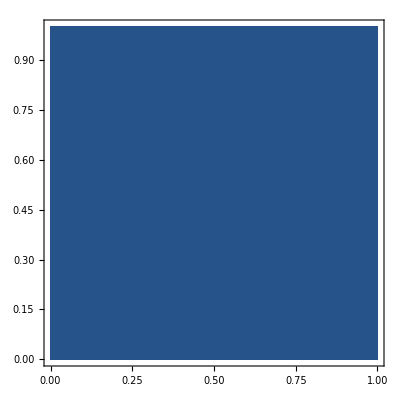

```mathematica
ContourPlot[0,{x,0,1},{y,0,1}]
```

### Darcy velocity :

```mathematica
KK:=perm*{{1, 0},{0, 1}}
```

```mathematica
-KK.{D[p[x,t],x],D[p[x,t],y]}//Simplify
```

{-perm t,0}

```mathematica
z[t_]:={-perm t,0}
```

```mathematica
ContourPlot[Sqrt[(-perm t)^2+(0)^2]/.{t->0.001, perm->1},{x,0,1},{y,0,1}]
```

-Graphics-

### Source term f :

```mathematica
Sigma[x,t]
```

{{-alpha t x+2 (λ+μ),0},{0,-alpha t x+2 (λ+μ)}}

```mathematica
-(D[-alpha t x+2 (λ+μ),x]+D[0,y])//Simplify
```

alpha t

```mathematica
f1[t_]:=alpha t
```

```mathematica
-(D[0,x]+D[-alpha t x+2 (λ+μ),y])//Simplify
```

0

```mathematica
f2:=0
```

### Source term q :

```mathematica
u[x,y]
```

{x,y}

```mathematica
z[t]
```

{-perm t,0}

```mathematica
D[c0 p[x,t]+alpha (D[x,x]+D[y,y]),t]+D[-perm t,x]+D[0,y]//Simplify
```

c0 x

```mathematica
FortranForm[c0 x/.{x->xx}]
```

c0*xx